Teukolsky > Teukolsky

# Solutions of the radial Teukolsky equation

This package is still in heavy development. This tutorial demonstrates some of the currently implemented features.

```mathematica
<<Teukolsky`
```

## Homogeneous solutions

```mathematica
R=TeukolskyRadial[-2,2,2,0.9`32,0.1`32]
```

TeukolskyRadialFunction[-2,2,2,0.90000000000000000000000000000000,0.10000000000000000000000000000000,<<>>]

```mathematica
R[10.]
R["In"][10.]
```

<|In→6168.99+2312.74 ⅈ,Up→569.699-527.776 ⅈ|>

6168.99+2312.74 ⅈ

```mathematica
R'[10.]
```

<|In→2451.2+1565.55 ⅈ,Up→-304.461+28.0435 ⅈ|>

```mathematica
R''[10.]
```

<|In→617.548+750.889 ⅈ,Up→-21.6604+19.9606 ⅈ|>

Using the field equation the package will allow you to take as many derivatives as you want

```mathematica
R'''''[10.]
```

<|In→-12.3909-2.46178 ⅈ,Up→-0.945864-2.57032 ⅈ|>

The homogeneous solutions are asymptotically unit normalized. e.g., lim_(r→∞) |R^up(r)/r^3|=1

```mathematica
Rdata=Table[{r,R["Up"][r]/r^3//ReIm}//Flatten,{r,10.,300.,1.}];
```

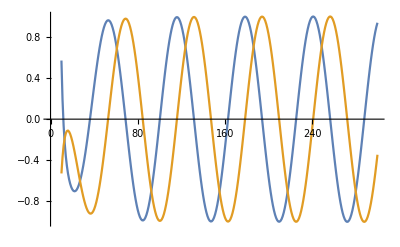

```mathematica
ListPlot[{Rdata[[;;,{1,2}]],Rdata[[;;,{1,3}]]},Joined->True]
```

## Renormalized angular momentum

There are two methods for computing the renormalized angular momentum. The series method is not yet fully implemented. The Monodromy method is usually robust so long as high precision values are entered.

```mathematica
RenormalizedAngularMomentum[1,2,1,0.9`32,0.25`32]
```

1.899810315856009681920152

## Fluxes (s=-2) circular, equatorial only

Currently the Teukolsky source has only been implemented for s=-2 and for a point mass in a circular, equatorial orbit.

```mathematica
a=0.9`32;
r0=10.`32;
```

```mathematica
orbit=KerrGeoOrbit[a,r0,0,1]
```

KerrGeoOrbitFunction[0.90000000000000000000000000000000,10.000000000000000000000000000000,0,1.,<<>>]

```mathematica
s=-2;l=2;m=2;n=0;k=0;
mode=TeukolskyPointParticleMode[s,l,m,n,k,orbit]
```

TeukolskyModeObject[-2,2,2,0,0,<<>>]

```mathematica
2mode["Fluxes"]
```

<|FluxInf→0.000057100937280781738,FluxHor→-1.3837279200122578×10^-7,FluxTotal→0.000056962564488780512|>

```mathematica
R=mode["Radial"]
```

TeukolskyRadialFunction[-2,2,2,0.90000000000000000000000000000000,0.06149536444857092909254283058,<<>>]

```mathematica
R[r0]
```

<|In→6413.70228963830465+705.66267889391545 ⅈ,Up→7622.4530901944146841-2568.3905799586499581 ⅈ|>